```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"out","poiseuille"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out/poiseuille

```mathematica
srtVelocitieFiles = Complement[FileNames["*velocity"], FileNames["*time"], FileNames["cumulant*"]];
cumulantVelocitieFiles = Complement[FileNames["*velocity"], FileNames["*time"], FileNames["srt*"]];
srtPressureFiles = Complement[FileNames["*density"], FileNames["*time"], FileNames["cumulant*"]];
cumulantPressureFiles = Complement[FileNames["*density"], FileNames["*time"], FileNames["srt*"]];
getLengths[thelist_]:=Read[StringToStream[#],Number]&/@Flatten[ StringDrop[#,6] &/@StringCases[thelist, RegularExpression["length([0-9]*)"]]] ;
lengths = getLengths[srtVelocitieFiles];
permutations = Ordering[lengths];
srtVelocitieFiles = srtVelocitieFiles[[permutations]];
cumulantVelocitieFiles = cumulantVelocitieFiles[[permutations]];
srtPressureFiles= srtPressureFiles[[permutations]];
cumulantPressureFiles = cumulantPressureFiles[[permutations]];
importData[list_]:=Import[#,"List"]& /@ list;
lengths = lengths[[permutations]];
myPlot[val_,labels_, drop_]:=ListLinePlot[Drop[val,drop], PlotLegends->Drop[labels,drop], PlotRange->All];
myPlotFromTo[val_,labels_, from_, to_]:=ListLinePlot[Part[val,from;;to], PlotLegends->Part[labels,from;;to], PlotRange->All];
getLengths[thelist_]:=Read[StringToStream[#],Number]&/@Flatten[ StringDrop[#,6] &/@StringCases[thelist, RegularExpression["length([0-9]*)"]]] ;
```

```mathematica
inletUlb004 ={0.0,0.00387812,0.01096953,0.01717452,0.02249307,0.02692521,0.03047091,0.03313019,0.03490305,0.03578947,0.03578947,0.03490305,0.03313019,0.03047091,0.02692521,0.02249307,0.01717452,0.01096953,0.00387812,0.0};
inlet = 0.25 inletUlb004;
```

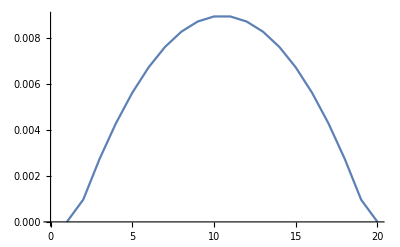

```mathematica
ListLinePlot[inlet]
```

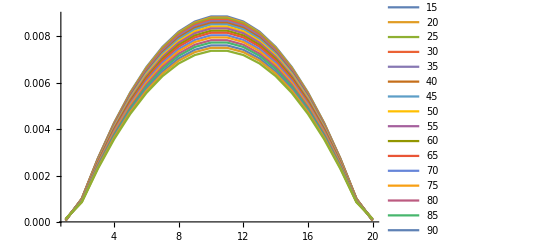

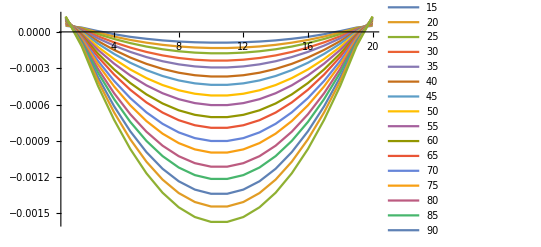

```mathematica
valuesSrtVelocity =  importData[srtVelocitieFiles];
errorSrtVelocity = (# -inlet) &/@ valuesSrtVelocity;
myPlot[valuesSrtVelocity,lengths,5]
myPlot[errorSrtVelocity,lengths,5]
```

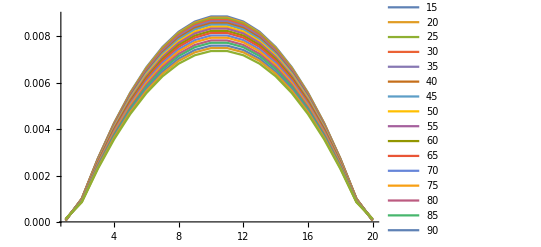

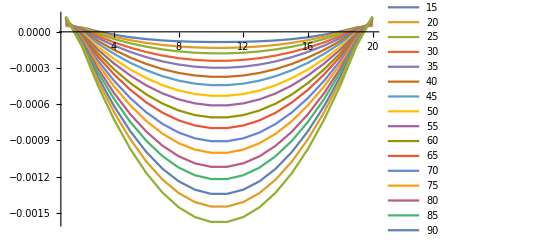

```mathematica
valuesCumulantVelocity = importData[cumulantVelocitieFiles];
errorCumulantVelocity = (# -inlet) &/@ valuesCumulantVelocity;
myPlot[valuesCumulantVelocity,lengths,5]
myPlot[errorCumulantVelocity,lengths,5]
```

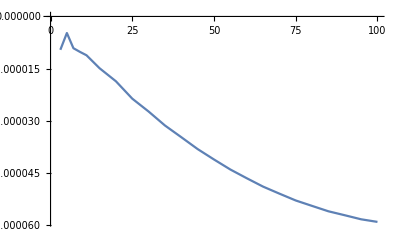

```mathematica
cumulantVsSrtVelocityError = errorCumulantVelocity-errorSrtVelocity;
cumulantVsSrtVelocityErrorTotal = Total /@ cumulantVsSrtVelocityError;
ListLinePlot[Transpose[{lengths,cumulantVsSrtVelocityErrorTotal}]]
```

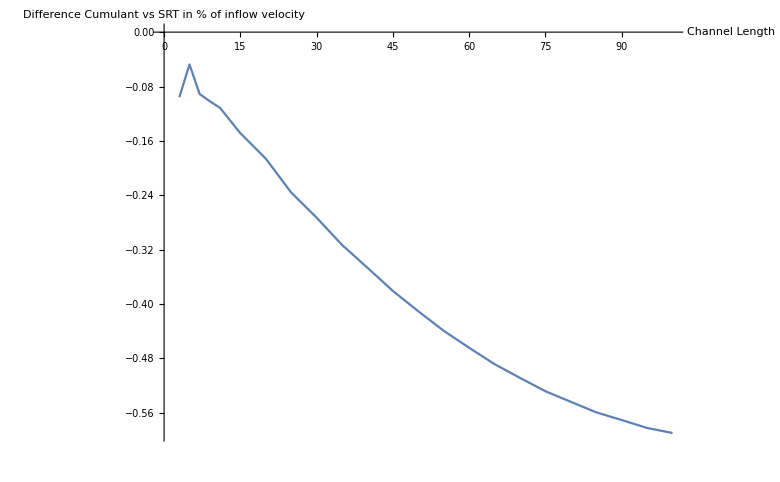

```mathematica
differenceInVelocity = Total /@(valuesCumulantVelocity - valuesSrtVelocity)/0.01*100;
ListLinePlot[Transpose[{lengths,differenceInVelocity}],AxesLabel->{"Channel Length","Difference Cumulant vs SRT
in % of inflow velocity"}]
```

```mathematica
pressureDifferences= valuesSrtPressure-valuesCumulantPressure;
plotNr = 18
ListLinePlot[Drop[pressureDifferences, 10], PlotLegends->Drop[lengths,10]]
ListLinePlot[pressureDifferences[[ plotNr]]]
```

18

Drop::drop: Cannot drop positions 1 through 10 in -valuesCumulantPressure+valuesSrtPressure.

Drop::drop: Cannot drop positions 1 through 10 in -1. valuesCumulantPressure+valuesSrtPressure.

General::stop: Further output of Drop::drop will be suppressed during this calculation.

ListLinePlot::lpn: Drop[-1. valuesCumulantPressure+valuesSrtPressure,10] is not a list of numbers or pairs of numbers.

ListLinePlot[Drop[-valuesCumulantPressure+valuesSrtPressure,10],PlotLegends→{40,45,50,55,60,65,70,75,80,85,90,95,100}]

Part::partw: Part 18 of -valuesCumulantPressure+valuesSrtPressure does not exist.

Part::partw: Part 18 of -1. valuesCumulantPressure+valuesSrtPressure does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: (-1. valuesCumulantPressure+valuesSrtPressure)⟦18⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[(-valuesCumulantPressure+valuesSrtPressure)⟦18⟧]